```mathematica
tick[n_]:=(1+Cos[π n])/2
```

```mathematica
tock[n_]:=1-tick[n]
```

```mathematica
even[n_]:=n/2
```

```mathematica
odd[n_]:=3n+1
```

```mathematica
realcol[n_]:=tick[n]even[n]+tock[n]odd[n]
```

```mathematica
realcol[n]
```

(1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])

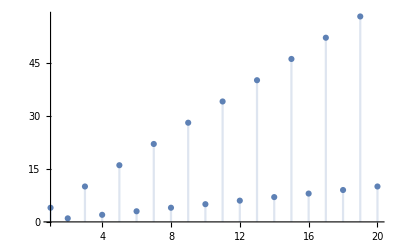

```mathematica
DiscretePlot[(1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π]),{n,1,20}]
```

```mathematica
col[n_]:=Piecewise[{{n/2, EvenQ[n]}, {3n+1, OddQ[n]}}]
```

```mathematica
realcol[n]==col[n]∧n∈
```

(1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])==0&&n∈ℤ&&n>0

```mathematica
Reduce[(1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])==0&&n∈Integers&&n>0]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[(1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])==0&&n∈ℤ&&n>0]

```mathematica
LanguageIdentify["Que?"]
```

Spanish

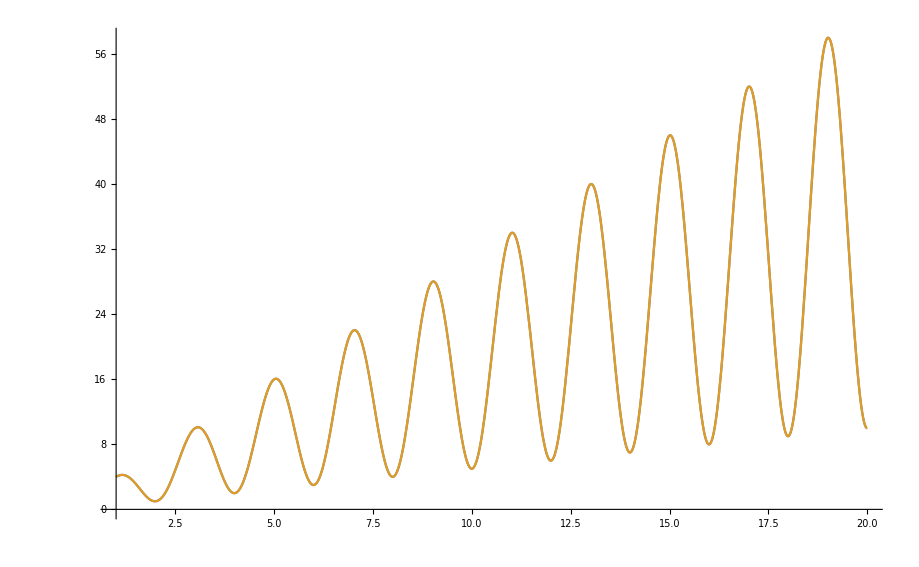

```mathematica
Plot[{
realcol[n],
(1+3 n) (1+1/2 (-1-Cos[n π]))+1/4 n (1+Cos[n π])
},{n,1,20}]
```

```mathematica
AxiomaticTheory["BooleanAxioms"]
```

{∀_{a,b}a⊗b==b⊗a,∀_{a,b}a⊕b==b⊕a,∀_{a,b}a⊗(b⊕b̄)==a,∀_{a,b}a⊕b⊗b̄==a,∀_{a,b,c}a⊗(b⊕c)==a⊗b⊕a⊗c,∀_{a,b,c}a⊕b⊗c==(a⊕b)⊗(a⊕c)}

```mathematica
FindEquationalProof[
∀_{a,b}OverBar[b⊕a]==b̄⊗ā,{
{∀_{a,b}a⊗b==b⊗a,∀_{a,b}a⊕b==b⊕a,∀_{a,b}a⊗(b⊕b̄)==a,∀_{a,b}a⊕b⊗b̄==a,∀_{a,b,c}a⊗(b⊕c)==a⊗b⊕a⊗c,∀_{a,b,c}a⊕b⊗c==(a⊕b)⊗(a⊕c)}
}]
```

ProofObject[…]

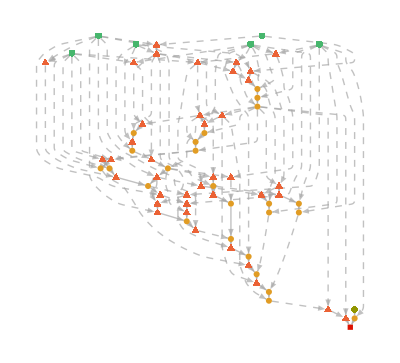

```mathematica
ProofObject[…]["ProofGraph"]
```

```mathematica
ProofObject[…]["ProofNotebook"]
```

Axiom 1
We are given that:
x1==x1⊗(x2⊕OverBar[x2])
Axiom 2
We are given that:
x1==x1⊕x2⊗OverBar[x2]
Axiom 3
We are given that:
x1⊗x2==x2⊗x1
Axiom 4
We are given that:
x1⊗(x2⊕x3)==x1⊗x2⊕x1⊗x3
Axiom 5
We are given that:
(x1⊕x2)⊗(x1⊕x3)==x1⊕x2⊗x3
Axiom 6
We are given that:
x1⊕x2==x2⊕x1
Hypothesis 1
We would like to show that:
b̄⊗ā==OverBar[b⊕a]
Critical Pair Lemma 1
The following expressions are equivalent:
(x1⊕OverBar[x1])⊗x2==x2
Proof
Note that the input for the rule:
x1_⊗x2_<->x2_⊗x1_
contains a subpattern of the form:
x1_⊗x2_
which can be unified with the input for the rule:
x1_⊗(x2_⊕OverBar[x2_])→x1
where these rules follow from Axiom 3 and Axiom 1 respectively.
Critical Pair Lemma 2
The following expressions are equivalent:
x1⊗(x2⊕OverBar[x1])==x1⊗x2
Proof
Note that the input for the rule:
x1_⊗x2_⊕x1_⊗x3_→x1⊗(x2⊕x3)
contains a subpattern of the form:
x1_⊗x2_⊕x1_⊗x3_
which can be unified with the input for the rule:
x1_⊕x2_⊗OverBar[x2_]→x1
where these rules follow from Axiom 4 and Axiom 2 respectively.
Critical Pair Lemma 3
The following expressions are equivalent:
x1⊗(x2⊕x3)==x2⊗x1⊕x1⊗x3
Proof
Note that the input for the rule:
x1_⊗x2_⊕x1_⊗x3_→x1⊗(x2⊕x3)
contains a subpattern of the form:
x1_⊗x2_
which can be unified with the input for the rule:
x1_⊗x2_<->x2_⊗x1_
where these rules follow from Axiom 4 and Axiom 3 respectively.
Critical Pair Lemma 4
The following expressions are equivalent:
x1⊕x2⊗OverBar[x1]==x1⊕x2
Proof
Note that the input for the rule:
(x1_⊕x2_)⊗(x1_⊕x3_)→x1⊕x2⊗x3
contains a subpattern of the form:
(x1_⊕x2_)⊗(x1_⊕x3_)
which can be unified with the input for the rule:
x1_⊗(x2_⊕OverBar[x2_])→x1
where these rules follow from Axiom 5 and Axiom 1 respectively.
Critical Pair Lemma 5
The following expressions are equivalent:
x1⊗OverBar[x1]⊕x2==x2
Proof
Note that the input for the rule:
x1_⊕x2_<->x2_⊕x1_
contains a subpattern of the form:
x1_⊕x2_
which can be unified with the input for the rule:
x1_⊕x2_⊗OverBar[x2_]→x1
where these rules follow from Axiom 6 and Axiom 2 respectively.
Critical Pair Lemma 6
The following expressions are equivalent:
x1⊕x2==x1⊕OverBar[x1]⊗x2
Proof
Note that the input for the rule:
(x1_⊕OverBar[x1_])⊗x2_→x2
contains a subpattern of the form:
(x1_⊕OverBar[x1_])⊗x2_
which can be unified with the input for the rule:
(x1_⊕x2_)⊗(x1_⊕x3_)→x1⊕x2⊗x3
where these rules follow from Critical Pair Lemma 1 and Axiom 5 respectively.
Critical Pair Lemma 7
The following expressions are equivalent:
x1⊗x2==x1⊗(OverBar[x1]⊕x2)
Proof
Note that the input for the rule:
x1_⊗OverBar[x1_]⊕x2_→x2
contains a subpattern of the form:
x1_⊗OverBar[x1_]⊕x2_
which can be unified with the input for the rule:
x1_⊗x2_⊕x1_⊗x3_→x1⊗(x2⊕x3)
where these rules follow from Critical Pair Lemma 5 and Axiom 4 respectively.
Critical Pair Lemma 8
The following expressions are equivalent:
x1⊕OverBar[OverBar[x1]]==x1
Proof
Note that the input for the rule:
x1_⊕OverBar[x1_]⊗x2_→x1⊕x2
contains a subpattern of the form:
x1_⊕OverBar[x1_]⊗x2_
which can be unified with the input for the rule:
x1_⊕x2_⊗OverBar[x2_]→x1
where these rules follow from Critical Pair Lemma 6 and Axiom 2 respectively.
Critical Pair Lemma 9
The following expressions are equivalent:
x1⊗OverBar[OverBar[OverBar[x1]]]==x1⊗OverBar[x1]
Proof
Note that the input for the rule:
x1_⊗(OverBar[x1_]⊕x2_)→x1⊗x2
contains a subpattern of the form:
OverBar[x1_]⊕x2_
which can be unified with the input for the rule:
x1_⊕OverBar[OverBar[x1_]]→x1
where these rules follow from Critical Pair Lemma 7 and Critical Pair Lemma 8 respectively.
Critical Pair Lemma 10
The following expressions are equivalent:
OverBar[OverBar[x1]]⊕x1==OverBar[OverBar[x1]]⊕x1⊗OverBar[x1]
Proof
Note that the input for the rule:
x1_⊕x2_⊗OverBar[x1_]→x1⊕x2
contains a subpattern of the form:
x2_⊗OverBar[x1_]
which can be unified with the input for the rule:
x1_⊗OverBar[OverBar[OverBar[x1_]]]→x1⊗OverBar[x1]
where these rules follow from Critical Pair Lemma 4 and Critical Pair Lemma 9 respectively.
Substitution Lemma 1
It can be shown that:
OverBar[OverBar[x1]]⊕x1==OverBar[OverBar[x1]]
Proof
We start by taking Critical Pair Lemma 10, and apply the substitution:
x1_⊕x2_⊗OverBar[x2_]→x1
which follows from Axiom 2.
Substitution Lemma 2
It can be shown that:
x1⊕OverBar[OverBar[x1]]==OverBar[OverBar[x1]]
Proof
We start by taking Substitution Lemma 1, and apply the substitution:
x1_⊕x2_→x2⊕x1
which follows from Axiom 6.
Substitution Lemma 3
It can be shown that:
x1==OverBar[OverBar[x1]]
Proof
We start by taking Substitution Lemma 2, and apply the substitution:
x1_⊕OverBar[OverBar[x1_]]→x1
which follows from Critical Pair Lemma 8.
Critical Pair Lemma 11
The following expressions are equivalent:
OverBar[x1]⊗x2==OverBar[x1]⊗(x1⊕x2)
Proof
Note that the input for the rule:
x1_⊗(OverBar[x1_]⊕x2_)→x1⊗x2
contains a subpattern of the form:
OverBar[x1_]
which can be unified with the input for the rule:
OverBar[OverBar[x1_]]→x1
where these rules follow from Critical Pair Lemma 7 and Substitution Lemma 3 respectively.
Critical Pair Lemma 12
The following expressions are equivalent:
OverBar[x1]⊕x2==OverBar[x1]⊕x1⊗x2
Proof
Note that the input for the rule:
x1_⊕OverBar[x1_]⊗x2_→x1⊕x2
contains a subpattern of the form:
OverBar[x1_]
which can be unified with the input for the rule:
OverBar[OverBar[x1_]]→x1
where these rules follow from Critical Pair Lemma 6 and Substitution Lemma 3 respectively.
Critical Pair Lemma 13
The following expressions are equivalent:
OverBar[x1]⊕x2==OverBar[x1]⊕x2⊗x1
Proof
Note that the input for the rule:
x1_⊕x2_⊗OverBar[x1_]→x1⊕x2
contains a subpattern of the form:
OverBar[x1_]
which can be unified with the input for the rule:
OverBar[OverBar[x1_]]→x1
where these rules follow from Critical Pair Lemma 4 and Substitution Lemma 3 respectively.
Critical Pair Lemma 14
The following expressions are equivalent:
x1⊕(x1⊕x2)==x1⊕OverBar[x1]⊗x2
Proof
Note that the input for the rule:
x1_⊕OverBar[x1_]⊗x2_→x1⊕x2
contains a subpattern of the form:
OverBar[x1_]⊗x2_
which can be unified with the input for the rule:
OverBar[x1_]⊗(x1_⊕x2_)→OverBar[x1]⊗x2
where these rules follow from Critical Pair Lemma 6 and Critical Pair Lemma 11 respectively.
Substitution Lemma 4
It can be shown that:
x1⊕(x1⊕x2)==x1⊕x2
Proof
We start by taking Critical Pair Lemma 14, and apply the substitution:
x1_⊕OverBar[x1_]⊗x2_→x1⊕x2
which follows from Critical Pair Lemma 6.
Critical Pair Lemma 15
The following expressions are equivalent:
x1⊕x2⊗(x1⊕x3)==(x1⊕x2)⊗(x1⊕x3)
Proof
Note that the input for the rule:
(x1_⊕x2_)⊗(x1_⊕x3_)→x1⊕x2⊗x3
contains a subpattern of the form:
x1_⊕x3_
which can be unified with the input for the rule:
x1_⊕(x1_⊕x2_)→x1⊕x2
where these rules follow from Axiom 5 and Substitution Lemma 4 respectively.
Substitution Lemma 5
It can be shown that:
x1⊕x2⊗(x1⊕x3)==x1⊕x2⊗x3
Proof
We start by taking Critical Pair Lemma 15, and apply the substitution:
(x1_⊕x2_)⊗(x1_⊕x3_)→x1⊕x2⊗x3
which follows from Axiom 5.
Critical Pair Lemma 16
The following expressions are equivalent:
OverBar[OverBar[x1]]⊗(x1⊗x2)==OverBar[OverBar[x1]]⊗(OverBar[x1]⊕x2)
Proof
Note that the input for the rule:
OverBar[x1_]⊗(x1_⊕x2_)→OverBar[x1]⊗x2
contains a subpattern of the form:
x1_⊕x2_
which can be unified with the input for the rule:
OverBar[x1_]⊕x1_⊗x2_→OverBar[x1]⊕x2
where these rules follow from Critical Pair Lemma 11 and Critical Pair Lemma 12 respectively.
Substitution Lemma 6
It can be shown that:
x1⊗(x1⊗x2)==OverBar[OverBar[x1]]⊗(OverBar[x1]⊕x2)
Proof
We start by taking Critical Pair Lemma 16, and apply the substitution:
OverBar[OverBar[x1_]]→x1
which follows from Substitution Lemma 3.
Substitution Lemma 7
It can be shown that:
x1⊗(x1⊗x2)==OverBar[OverBar[x1]]⊗x2
Proof
We start by taking Substitution Lemma 6, and apply the substitution:
OverBar[x1_]⊗(x1_⊕x2_)→OverBar[x1]⊗x2
which follows from Critical Pair Lemma 11.
Substitution Lemma 8
It can be shown that:
x1⊗(x1⊗x2)==x1⊗x2
Proof
We start by taking Substitution Lemma 7, and apply the substitution:
OverBar[OverBar[x1_]]→x1
which follows from Substitution Lemma 3.
Critical Pair Lemma 17
The following expressions are equivalent:
x1⊗(x1⊗x2⊕x3)==x1⊗x2⊕x1⊗x3
Proof
Note that the input for the rule:
x1_⊗x2_⊕x1_⊗x3_→x1⊗(x2⊕x3)
contains a subpattern of the form:
x1_⊗x2_
which can be unified with the input for the rule:
x1_⊗(x1_⊗x2_)→x1⊗x2
where these rules follow from Axiom 4 and Substitution Lemma 8 respectively.
Substitution Lemma 9
It can be shown that:
x1⊗(x1⊗x2⊕x3)==x1⊗(x2⊕x3)
Proof
We start by taking Critical Pair Lemma 17, and apply the substitution:
x1_⊗x2_⊕x1_⊗x3_→x1⊗(x2⊕x3)
which follows from Axiom 4.
Critical Pair Lemma 18
The following expressions are equivalent:
x1⊗(x2⊕x1⊗x3)==x1⊗x2⊕x1⊗x3
Proof
Note that the input for the rule:
x1_⊗x2_⊕x1_⊗x3_→x1⊗(x2⊕x3)
contains a subpattern of the form:
x1_⊗x3_
which can be unified with the input for the rule:
x1_⊗(x1_⊗x2_)→x1⊗x2
where these rules follow from Axiom 4 and Substitution Lemma 8 respectively.
Substitution Lemma 10
It can be shown that:
x1⊗(x2⊕x1⊗x3)==x1⊗(x2⊕x3)
Proof
We start by taking Critical Pair Lemma 18, and apply the substitution:
x1_⊗x2_⊕x1_⊗x3_→x1⊗(x2⊕x3)
which follows from Axiom 4.
Critical Pair Lemma 19
The following expressions are equivalent:
x1⊕x2⊗OverBar[x2]==x1⊕x2⊗x1
Proof
Note that the input for the rule:
x1_⊕x2_⊗(x1_⊕x3_)→x1⊕x2⊗x3
contains a subpattern of the form:
x2_⊗(x1_⊕x3_)
which can be unified with the input for the rule:
x1_⊗(x2_⊕OverBar[x1_])→x1⊗x2
where these rules follow from Substitution Lemma 5 and Critical Pair Lemma 2 respectively.
Substitution Lemma 11
It can be shown that:
x1==x1⊕x2⊗x1
Proof
We start by taking Critical Pair Lemma 19, and apply the substitution:
x1_⊕x2_⊗OverBar[x2_]→x1
which follows from Axiom 2.
Critical Pair Lemma 20
The following expressions are equivalent:
x1⊗OverBar[x1]==x2⊗(x1⊗OverBar[x1])
Proof
Note that the input for the rule:
x1_⊕x2_⊗x1_→x1
contains a subpattern of the form:
x1_⊕x2_⊗x1_
which can be unified with the input for the rule:
x1_⊗OverBar[x1_]⊕x2_→x2
where these rules follow from Substitution Lemma 11 and Critical Pair Lemma 5 respectively.
Critical Pair Lemma 21
The following expressions are equivalent:
x1==x1⊕x1⊗x2
Proof
Note that the input for the rule:
x1_⊕x2_⊗x1_→x1
contains a subpattern of the form:
x2_⊗x1_
which can be unified with the input for the rule:
x1_⊗x2_<->x2_⊗x1_
where these rules follow from Substitution Lemma 11 and Axiom 3 respectively.
Critical Pair Lemma 22
The following expressions are equivalent:
OverBar[x1]⊗(x2⊗x1)==OverBar[x1]⊗x1
Proof
Note that the input for the rule:
OverBar[x1_]⊗(x1_⊕x2_)→OverBar[x1]⊗x2
contains a subpattern of the form:
x1_⊕x2_
which can be unified with the input for the rule:
x1_⊕x2_⊗x1_→x1
where these rules follow from Critical Pair Lemma 11 and Substitution Lemma 11 respectively.
Critical Pair Lemma 23
The following expressions are equivalent:
x1⊗(OverBar[x1]⊗x2)==x1⊗OverBar[x1]
Proof
Note that the input for the rule:
x1_⊗(OverBar[x1_]⊕x2_)→x1⊗x2
contains a subpattern of the form:
OverBar[x1_]⊕x2_
which can be unified with the input for the rule:
x1_⊕x1_⊗x2_→x1
where these rules follow from Critical Pair Lemma 7 and Critical Pair Lemma 21 respectively.
Substitution Lemma 12
It can be shown that:
OverBar[x1]⊗(x2⊗x1)==x1⊗OverBar[x1]
Proof
We start by taking Critical Pair Lemma 22, and apply the substitution:
x1_⊗x2_→x2⊗x1
which follows from Axiom 3.
Critical Pair Lemma 24
The following expressions are equivalent:
(x1⊗x2)⊗OverBar[x1⊗x2]==OverBar[x1⊗x2]⊗(x2⊗OverBar[x2])
Proof
Note that the input for the rule:
OverBar[x1_]⊗(x2_⊗x1_)→x1⊗OverBar[x1]
contains a subpattern of the form:
x2_⊗x1_
which can be unified with the input for the rule:
OverBar[x1_]⊗(x2_⊗x1_)→x1⊗OverBar[x1]
where these rules follow from Substitution Lemma 12 and Substitution Lemma 12 respectively.
Substitution Lemma 13
It can be shown that:
(x1⊗x2)⊗OverBar[x1⊗x2]==x2⊗OverBar[x2]
Proof
We start by taking Critical Pair Lemma 24, and apply the substitution:
x1_⊗(x2_⊗OverBar[x2_])→x2⊗OverBar[x2]
which follows from Critical Pair Lemma 20.
Critical Pair Lemma 25
The following expressions are equivalent:
OverBar[x1⊗x2]⊕OverBar[x2]==OverBar[x1⊗x2]⊕x2⊗OverBar[x2]
Proof
Note that the input for the rule:
OverBar[x1_]⊕x2_⊗x1_→OverBar[x1]⊕x2
contains a subpattern of the form:
x2_⊗x1_
which can be unified with the input for the rule:
OverBar[x1_]⊗(x2_⊗x1_)→x1⊗OverBar[x1]
where these rules follow from Critical Pair Lemma 13 and Substitution Lemma 12 respectively.
Substitution Lemma 14
It can be shown that:
OverBar[x1⊗x2]⊕OverBar[x2]==OverBar[x1⊗x2]
Proof
We start by taking Critical Pair Lemma 25, and apply the substitution:
x1_⊕x2_⊗OverBar[x2_]→x1
which follows from Axiom 2.
Critical Pair Lemma 26
The following expressions are equivalent:
OverBar[OverBar[x1]⊗x2]⊕x1==OverBar[OverBar[x1]⊗x2]⊕x1⊗OverBar[x1]
Proof
Note that the input for the rule:
OverBar[x1_]⊕x2_⊗x1_→OverBar[x1]⊕x2
contains a subpattern of the form:
x2_⊗x1_
which can be unified with the input for the rule:
x1_⊗(OverBar[x1_]⊗x2_)→x1⊗OverBar[x1]
where these rules follow from Critical Pair Lemma 13 and Critical Pair Lemma 23 respectively.
Substitution Lemma 15
It can be shown that:
OverBar[OverBar[x1]⊗x2]⊕x1==OverBar[OverBar[x1]⊗x2]
Proof
We start by taking Critical Pair Lemma 26, and apply the substitution:
x1_⊕x2_⊗OverBar[x2_]→x1
which follows from Axiom 2.
Substitution Lemma 16
It can be shown that:
OverBar[x1]⊕OverBar[x2⊗x1]==OverBar[x2⊗x1]
Proof
We start by taking Substitution Lemma 14, and apply the substitution:
x1_⊕x2_→x2⊕x1
which follows from Axiom 6.
Critical Pair Lemma 27
The following expressions are equivalent:
x1⊗(x2⊕x2⊗x3)==x1⊗(x2⊗(x1⊕x3))
Proof
Note that the input for the rule:
x1_⊗(x1_⊗x2_⊕x3_)→x1⊗(x2⊕x3)
contains a subpattern of the form:
x1_⊗x2_⊕x3_
which can be unified with the input for the rule:
x1_⊗x2_⊕x2_⊗x3_→x2⊗(x1⊕x3)
where these rules follow from Substitution Lemma 9 and Critical Pair Lemma 3 respectively.
Substitution Lemma 17
It can be shown that:
x1⊗x2==x1⊗(x2⊗(x1⊕x3))
Proof
We start by taking Critical Pair Lemma 27, and apply the substitution:
x1_⊕x1_⊗x2_→x1
which follows from Critical Pair Lemma 21.
Critical Pair Lemma 28
The following expressions are equivalent:
x1⊗x2==x1⊗((x1⊕x3)⊗x2)
Proof
Note that the input for the rule:
x1_⊗(x2_⊗(x1_⊕x3_))→x1⊗x2
contains a subpattern of the form:
x2_⊗(x1_⊕x3_)
which can be unified with the input for the rule:
x1_⊗x2_<->x2_⊗x1_
where these rules follow from Substitution Lemma 17 and Axiom 3 respectively.
Critical Pair Lemma 29
The following expressions are equivalent:
x1⊗x2==x1⊗(x2⊗(x3⊕x1))
Proof
Note that the input for the rule:
x1_⊗(x2_⊗(x1_⊕x3_))→x1⊗x2
contains a subpattern of the form:
x1_⊕x3_
which can be unified with the input for the rule:
x1_⊕x2_<->x2_⊕x1_
where these rules follow from Substitution Lemma 17 and Axiom 6 respectively.
Critical Pair Lemma 30
The following expressions are equivalent:
x1⊗x2==x1⊗((x3⊕x1)⊗x2)
Proof
Note that the input for the rule:
x1_⊗((x1_⊕x2_)⊗x3_)→x1⊗x3
contains a subpattern of the form:
x1_⊕x2_
which can be unified with the input for the rule:
x1_⊕x2_<->x2_⊕x1_
where these rules follow from Critical Pair Lemma 28 and Axiom 6 respectively.
Critical Pair Lemma 31
The following expressions are equivalent:
(x1⊗x2)⊗x3==(x1⊗x2)⊗(x3⊗x1)
Proof
Note that the input for the rule:
x1_⊗(x2_⊗(x3_⊕x1_))→x1⊗x2
contains a subpattern of the form:
x3_⊕x1_
which can be unified with the input for the rule:
x1_⊕x1_⊗x2_→x1
where these rules follow from Critical Pair Lemma 29 and Critical Pair Lemma 21 respectively.
Critical Pair Lemma 32
The following expressions are equivalent:
(x1⊗x2)⊗x3==(x1⊗x2)⊗(x2⊗x3)
Proof
Note that the input for the rule:
x1_⊗((x2_⊕x1_)⊗x3_)→x1⊗x3
contains a subpattern of the form:
x2_⊕x1_
which can be unified with the input for the rule:
x1_⊕x2_⊗x1_→x1
where these rules follow from Critical Pair Lemma 30 and Substitution Lemma 11 respectively.
Substitution Lemma 18
It can be shown that:
x1⊕OverBar[OverBar[x1]⊗x2]==OverBar[OverBar[x1]⊗x2]
Proof
We start by taking Substitution Lemma 15, and apply the substitution:
x1_⊕x2_→x2⊕x1
which follows from Axiom 6.
Critical Pair Lemma 33
The following expressions are equivalent:
(x1⊗x2)⊗x3==(x3⊗x1)⊗(x1⊗x2)
Proof
Note that the input for the rule:
(x1_⊗x2_)⊗(x3_⊗x1_)→(x1⊗x2)⊗x3
contains a subpattern of the form:
(x1_⊗x2_)⊗(x3_⊗x1_)
which can be unified with the input for the rule:
x1_⊗x2_<->x2_⊗x1_
where these rules follow from Critical Pair Lemma 31 and Axiom 3 respectively.
Substitution Lemma 19
It can be shown that:
(x1⊗x2)⊗x3==(x3⊗x1)⊗x2
Proof
We start by taking Critical Pair Lemma 33, and apply the substitution:
(x1_⊗x2_)⊗(x2_⊗x3_)→(x1⊗x2)⊗x3
which follows from Critical Pair Lemma 32.
Critical Pair Lemma 34
The following expressions are equivalent:
(x1⊗x2)⊗x3==x1⊗(x2⊗x3)
Proof
Note that the input for the rule:
(x1_⊗x2_)⊗x3_<->(x3_⊗x1_)⊗x2_
contains a subpattern of the form:
(x1_⊗x2_)⊗x3_
which can be unified with the input for the rule:
x1_⊗x2_<->x2_⊗x1_
where these rules follow from Substitution Lemma 19 and Axiom 3 respectively.
Substitution Lemma 20
It can be shown that:
x1⊗(x2⊗OverBar[x1⊗x2])==x2⊗OverBar[x2]
Proof
We start by taking Substitution Lemma 13, and apply the substitution:
(x1_⊗x2_)⊗x3_→x1⊗(x2⊗x3)
which follows from Critical Pair Lemma 34.
Critical Pair Lemma 35
The following expressions are equivalent:
x1⊕x2⊗OverBar[OverBar[x1]⊗x2]==x1⊕x2⊗OverBar[x2]
Proof
Note that the input for the rule:
x1_⊕OverBar[x1_]⊗x2_→x1⊕x2
contains a subpattern of the form:
OverBar[x1_]⊗x2_
which can be unified with the input for the rule:
x1_⊗(x2_⊗OverBar[x1_⊗x2_])→x2⊗OverBar[x2]
where these rules follow from Critical Pair Lemma 6 and Substitution Lemma 20 respectively.
Substitution Lemma 21
It can be shown that:
x1⊕x2⊗OverBar[OverBar[x1]⊗x2]==x1
Proof
We start by taking Critical Pair Lemma 35, and apply the substitution:
x1_⊕x2_⊗OverBar[x2_]→x1
which follows from Axiom 2.
Critical Pair Lemma 36
The following expressions are equivalent:
x1⊗(x2⊕OverBar[OverBar[x2]⊗x1])==x1⊗x2
Proof
Note that the input for the rule:
x1_⊗(x2_⊕x1_⊗x3_)→x1⊗(x2⊕x3)
contains a subpattern of the form:
x2_⊕x1_⊗x3_
which can be unified with the input for the rule:
x1_⊕x2_⊗OverBar[OverBar[x1_]⊗x2_]→x1
where these rules follow from Substitution Lemma 10 and Substitution Lemma 21 respectively.
Substitution Lemma 22
It can be shown that:
x1⊗OverBar[OverBar[x2]⊗x1]==x1⊗x2
Proof
We start by taking Critical Pair Lemma 36, and apply the substitution:
x1_⊕OverBar[OverBar[x1_]⊗x2_]→OverBar[OverBar[x1]⊗x2]
which follows from Substitution Lemma 18.
Critical Pair Lemma 37
The following expressions are equivalent:
OverBar[x1]⊕OverBar[OverBar[x2]⊗x1]==OverBar[x1]⊕x1⊗x2
Proof
Note that the input for the rule:
OverBar[x1_]⊕x1_⊗x2_→OverBar[x1]⊕x2
contains a subpattern of the form:
x1_⊗x2_
which can be unified with the input for the rule:
x1_⊗OverBar[OverBar[x2_]⊗x1_]→x1⊗x2
where these rules follow from Critical Pair Lemma 12 and Substitution Lemma 22 respectively.
Substitution Lemma 23
It can be shown that:
OverBar[OverBar[x1]⊗x2]==OverBar[x2]⊕x2⊗x1
Proof
We start by taking Critical Pair Lemma 37, and apply the substitution:
OverBar[x1_]⊕OverBar[x2_⊗x1_]→OverBar[x2⊗x1]
which follows from Substitution Lemma 16.
Substitution Lemma 24
It can be shown that:
OverBar[OverBar[x1]⊗x2]==OverBar[x2]⊕x1
Proof
We start by taking Substitution Lemma 23, and apply the substitution:
OverBar[x1_]⊕x1_⊗x2_→OverBar[x1]⊕x2
which follows from Critical Pair Lemma 12.
Critical Pair Lemma 38
The following expressions are equivalent:
OverBar[x1]⊗x2==OverBar[OverBar[x2]⊕x1]
Proof
Note that the input for the rule:
OverBar[OverBar[x1_]]→x1
contains a subpattern of the form:
OverBar[x1_]
which can be unified with the input for the rule:
OverBar[OverBar[x1_]⊗x2_]→OverBar[x2]⊕x1
where these rules follow from Substitution Lemma 3 and Substitution Lemma 24 respectively.
Critical Pair Lemma 39
The following expressions are equivalent:
OverBar[x1]⊗OverBar[x2]==OverBar[x2⊕x1]
Proof
Note that the input for the rule:
OverBar[OverBar[x1_]⊕x2_]→OverBar[x2]⊗x1
contains a subpattern of the form:
OverBar[x1_]
which can be unified with the input for the rule:
OverBar[OverBar[x1_]]→x1
where these rules follow from Critical Pair Lemma 38 and Substitution Lemma 3 respectively.
Substitution Lemma 25
It can be shown that:
b̄⊗ā==OverBar[a⊕b]
Proof
We start by taking Hypothesis 1, and apply the substitution:
x1_⊕x2_→x2⊕x1
which follows from Axiom 6.
Conclusion 1
We obtain the conclusion:
True
Proof
Take Substitution Lemma 25, and apply the substitution:
OverBar[x1_]⊗OverBar[x2_]→OverBar[x2⊕x1]
which follows from Critical Pair Lemma 39.

```mathematica
Graph[{
n->e,
n->o,
e->n,
o->e
}]
```

-Graphics-

```mathematica
Graph[{
n->e,
n->o,
e->n,
o->e
},{
down,
up,
down,
up
}]
```

Graph[{n→e,n→o,e→n,o→e},{down,up,down,up}]

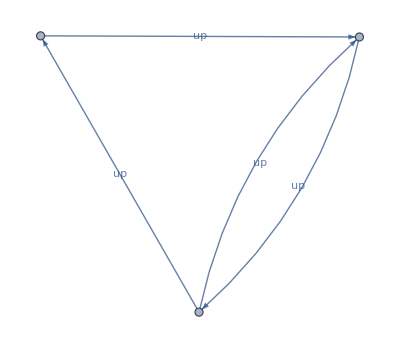

```mathematica
Graph[{
n->e,
n->o,
e->n,
o->e
},EdgeLabels->{
down,
up,
down,
up
}]
```

```mathematica
Graph[{
e->o,
e->e,
o->e
}]
```

-Graphics-

```mathematica
Graph[{
e->o,
e->e,
o->e
}]
```